Custom Histogram From Imported Data

```mathematica
InputField[Dynamic[subdirectory],String]
```

Here you can import data from a .txt file to graph a histogram. Enter the file path and the file name (with extension) below and enter your parameters.

File Path:

```mathematica
InputField[Dynamic[subdirectory], String]
```

```mathematica
InputField[Dynamic[filename],String]
```

File Name:

```mathematica
InputField[Dynamic[IncomingData],String]
```

```mathematica
SetDirectory[subdirectory];
IncomingData=Flatten[ReadList[IncomingData,{Number}],1];
FileLength=Length[IncomingData];
Avg=Total[IncomingData]/FileLength;
Deviance=IncomingData-Avg; StdDeviation=√(Total[Deviance^2]/FileLength);
StandardError=StdDeviation/Sqrt[FileLength];
```

```mathematica
InputField[Dynamic[StartingPoint]]
```

Starting Point:

```mathematica
InputField[Dynamic[StartingPoint]]
```

```mathematica
InputField[Dynamic[BinSize]]
```

BinSize:

```mathematica
InputField[Dynamic[BinSize]]
```

```mathematica
InputField[Dynamic[NumberOfBins]]
```

Number Of Bins:

```mathematica
InputField[Dynamic[NumberOfBins]]
```

```mathematica
InputField[Dynamic[AxisLabelX],String]
```

X-Axis Label:

```mathematica
InputField[Dynamic[AxisLabelX], String]
```

```mathematica
InputField[Dynamic[AxisLabelY],String]
```

Y-Axis Label:

```mathematica
InputField[Dynamic[AxisLabelY], String]
```

Plot Label :

```mathematica
InputField[Dynamic[HistLabel], String]
```

Plot!

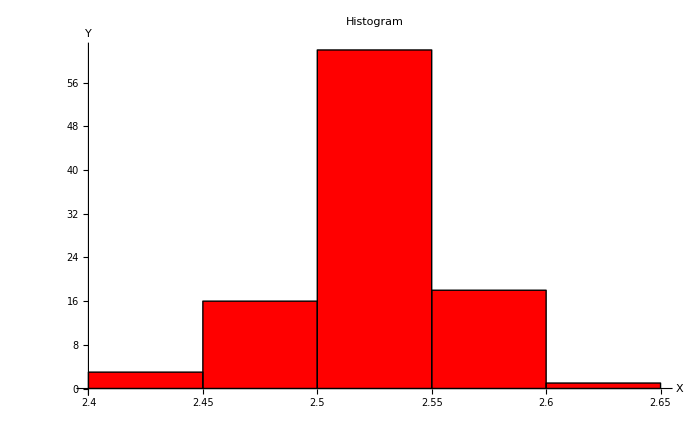

```mathematica
Midpoints=Table[i,{i,StartingPoint+BinSize/2,StartingPoint+NumberOfBins*BinSize,BinSize}];
Histogram[IncomingData,HistogramCategories->Range[StartingPoint,StartingPoint+NumberOfBins*BinSize,BinSize],
AxesLabel->{AxisLabelX,AxisLabelY},PlotLabel->HistLabel,ImageSize->700]
```

```mathematica
Print["Max=",Max[IncomingData]];
Print["Min=",Min[IncomingData]];
Print["Average=",Avg];
Print["σ=",StdDeviation];
Print["Standard Error=",StandardError];
```

Max=2.633

Min=2.438

Average=2.52248

σ=0.0326927

Standard Error=0.00326927

```mathematica
<<Graphics`Graphics`;<<Statistics`DataManipulation`
```

General::obspkg: Graphics`Graphics` is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

General::obspkg: Statistics`DataManipulation` is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.